```mathematica
backgroundsolution[args_]:= Module[
{startI = 0,
endI = 1,
ϕcosmological = 0,
k = 4 Pi^2},
Shooter = args[[2]];
ϕ0 = args[[1]];
backgroundsolutioninterior= NDSolve[{D[u[r],r,r] == -k u[r],u'[startI] ==√k,u[startI] ==  ϕ0},
u,{r,startI,endI}];
Proximity= (u[endI]/.backgroundsolutioninterior) -ϕcosmological;
If[Shooter,Prepend[Proximity,ϕ0],backgroundsolutioninterior]
]
```

```mathematica
solutions = Table[backgroundsolution[{x,True}],{x,Range[-1,2,.1]}];
```

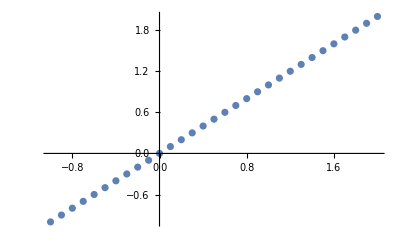

```mathematica
ListPlot[solutions]
```

```mathematica
sol = backgroundsolution[{0,False}]
```

{{u→InterpolatingFunction[{{0., 1.}}, <>]}}

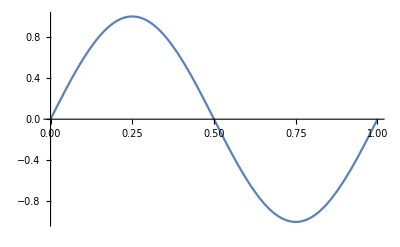

```mathematica
Plot[u[r]/.sol,{r,0,1}]
```